```mathematica
(*spline*)
competitive={1.21388*^07,4.64632*^06,3.47496*^06,3.22095*^06,3.22905*^06,3.90802*^06,2.84327*^06};
monopoly={1.25823*^07,4.77103*^06,3.58568*^06,3.31037*^06,3.28174*^06,4.06436*^06,2.89229*^06};
```

```mathematica
(*linear*)
(*competitive={1.17038*^07, 4.57596*^06 ,3.41347*^06, 3.16644*^06, 3.17113*^06, 3.84277*^06,2.78898*^06};
monopoly={1.28725*^07, 4.88604*^06, 3.6964*^06, 3.401*^06,3.34444*^06, 4.21046*^06, 2.95316*^06};*)
```

```mathematica
names={"Saudi Arabia","Iran","Iraq","Kuwait","UAE","Venezula","Nigeria"};
```

```mathematica
totComp=Plus@@competitive;
totMon=Plus@@monopoly;
```

```mathematica
range=Max[competitive,monopoly]
```

1.25823×10^7

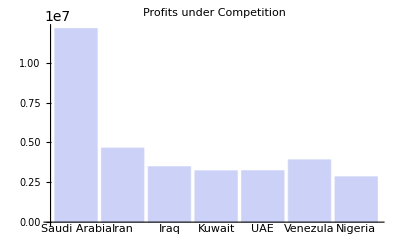

```mathematica
BarChart[competitive,ChartLabels->names,PlotLabel->"Profits under Competition",PlotRange->{Automatic,range}]
```

```mathematica
PieChart[competitive,ChartLabels->names,PlotLabel->"Profits under Competition"]
```

-Graphics-

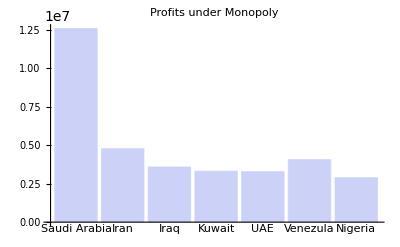

```mathematica
BarChart[monopoly,ChartLabels->names,PlotLabel->"Profits under Monopoly",PlotRange->{Automatic,range}]
```

```mathematica
PieChart[monopoly,ChartLabels->names,PlotLabel->"Profits under Monopoly"]
```

-Graphics-

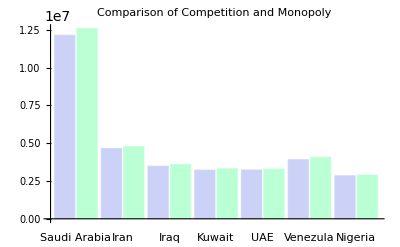

```mathematica
BarChart[{competitive,monopoly}//Transpose,ChartLabels->{names,{"",""}},PlotLabel->"Comparison of Competition and Monopoly",PlotRange->{Automatic,range}]
```

```mathematica
stackedProfits=Transpose[{competitive,monopoly-competitive}]
```

{{1.21388×10^7,443500.},{4.64632×10^6,124710.},{3.47496×10^6,110720.},{3.22095×10^6,89420.},{3.22905×10^6,52690.},{3.90802×10^6,156340.},{2.84327×10^6,49020.}}

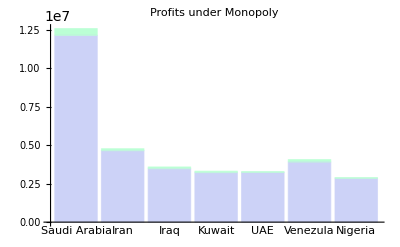

```mathematica
BarChart[stackedProfits,ChartLabels->{names,{"",""}},PlotLabel->"Profits under Monopoly",PlotRange->{Automatic,range},ChartLayout->"Stacked"]
```

```mathematica
pct=(monopoly/competitive)~Join~{totMon/totComp};
pct=pct-1;
pct=pct*100;
```

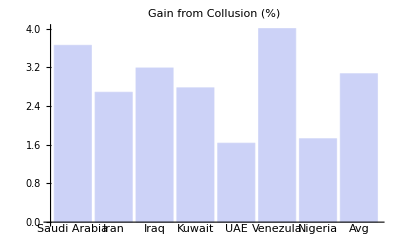

```mathematica
BarChart[pct,ChartLabels->names~Join~{"Avg"},PlotLabel->"Gain from Collusion (%)"]
```

```mathematica
PieChart[pct[[1;;-2]],ChartLabels->names,PlotLabel->"Gain from Collusion (%)"]
```

-Graphics-